# Математическа статистика 2024-2025 учебна година доц. Петър Копанов

Регресионен анализ

## Проста линейна регресия

Обеми на извадките : 20   ,  20

FittedModel[41.7498+3.73663 x]

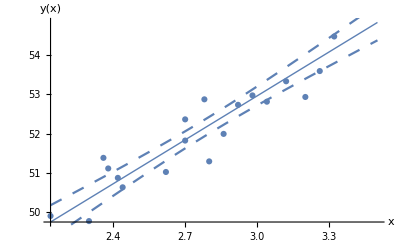

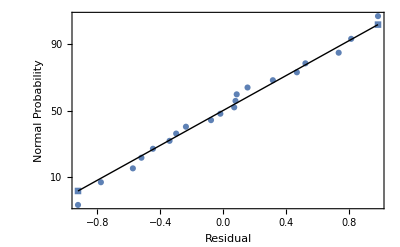

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
	(*    Задаване на извадките   *) 

xx={2.38,2.44,2.70,2.98,3.32,3.12,2.14,2.86,3.50,3.20,2.78,2.70,2.36,2.42,2.62,2.80,2.92,3.04,3.26,2.30};
yy={51.11,50.63,51.82,52.97,54.47,53.33,49.90,51.99,55.81,52.93,52.87,52.36,51.38,50.87,51.02,51.29,52.73,52.81,53.59,49.77};
Print ["Обеми на извадките : ", Length[xx], "   ,  ", Length[yy]]
pts=Table[{xx[[n]],yy[[n]]},{n,1,Length[xx]}];
modl=LinearModelFit[pts,x,x,ConfidenceLevel->0.90]
bands=modl["MeanPredictionBands"];
xm=Min[xx];xmx=Max[xx];
Show[Plot[modl[x],{x,xm,xmx},PlotStyle->Thick,AxesLabel->{"x","y(x)"}],ListPlot[pts,PlotMarkers->Automatic],Plot[{bands[[1]],bands[[2]]}/.x->f,{f,xm,xmx},PlotStyle->Dashing[Medium]]]
ProbabilityScalePlot[modl["FitResiduals"],"Normal",PlotMarkers->Automatic,FrameLabel->{"Residual","Normal Probability"}]
```

## Нелинейна регресия 1 Логаритмичен модел

Обеми на извадките : 20   ,  20

NonlinearModelFit::nrlnum: The function value {0.140242+0. ⅈ,0.878133+0. ⅈ,0.413304+0. ⅈ,-0.250662+0. ⅈ,-1.32682+0. ⅈ,-0.420608+0. ⅈ,-1.08969+3.14159 ⅈ,0.542437+0. ⅈ,-2.48413+0. ⅈ,0.0774935+0. ⅈ,-0.478527+0. ⅈ,-0.126696+0. ⅈ,-0.230766+0. ⅈ,0.558502+0. ⅈ,1.0325+0. ⅈ,1.13816+0. ⅈ,-0.10088+0. ⅈ,-0.00601643+0. ⅈ,-0.513086+0. ⅈ,1.00491+0. ⅈ} is not a list of real numbers with dimensions {20} at {a,b,c} = {-6.2284×10^22,-1.98516×10^22,2.25322×10^22}.

FittedModel[Log[-6.2284×10^22-1.98516×10^22 x+2.25322×10^22 x^2]]

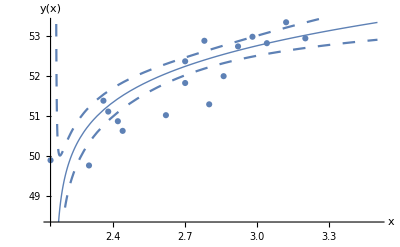

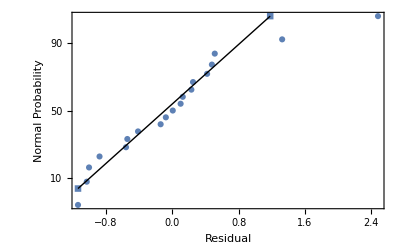

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
	(*    Задаване на извадките   *) 

xx={2.38,2.44,2.70,2.98,3.32,3.12,2.14,2.86,3.50,3.20,2.78,2.70,2.36,2.42,2.62,2.80,2.92,3.04,3.26,2.30};
yy={51.11,50.63,51.82,52.97,54.47,53.33,49.90,51.99,55.81,52.93,52.87,52.36,51.38,50.87,51.02,51.29,52.73,52.81,53.59,49.77};
Print ["Обеми на извадките : ", Length[xx], "   ,  ", Length[yy]]
pts=Table[{xx[[n]],yy[[n]]},{n,1,Length[xx]}];
modl=NonlinearModelFit[pts,Log[a +b x + c x^2],{a,b, c},x,ConfidenceLevel->0.90]
bands=modl["MeanPredictionBands"];
xm=Min[xx];xmx=Max[xx];
Show[Plot[modl[x],{x,xm,xmx},PlotStyle->Thick,AxesLabel->{"x","y(x)"}],ListPlot[pts,PlotMarkers->Automatic],Plot[{bands[[1]],bands[[2]]}/.x->f,{f,xm,xmx},PlotStyle->Dashing[Medium]]]
ProbabilityScalePlot[modl["FitResiduals"],"Normal",PlotMarkers->Automatic,FrameLabel->{"Residual","Normal Probability"}]
```

## Нелинейна регресия 2 Полиномен модел

Обеми на извадките : 20   ,  20

FittedModel[-23.7254+78.4644 x-28.0297 x^2+3.45501 x^3]

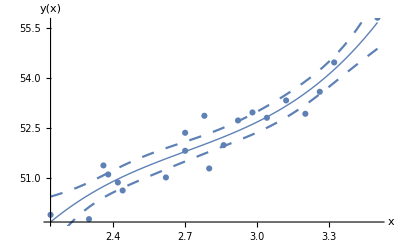

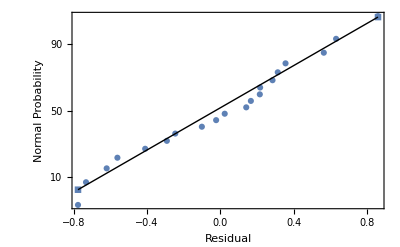

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
	(*    Задаване на извадките   *) 

xx={2.38,2.44,2.70,2.98,3.32,3.12,2.14,2.86,3.50,3.20,2.78,2.70,2.36,2.42,2.62,2.80,2.92,3.04,3.26,2.30};
yy={51.11,50.63,51.82,52.97,54.47,53.33,49.90,51.99,55.81,52.93,52.87,52.36,51.38,50.87,51.02,51.29,52.73,52.81,53.59,49.77};
Print ["Обеми на извадките : ", Length[xx], "   ,  ", Length[yy]]
pts=Table[{xx[[n]],yy[[n]]},{n,1,Length[xx]}];
modl=NonlinearModelFit[pts,a +b x+c x^2 + d x^3,{a,b, c, d},x,ConfidenceLevel->0.90]
bands=modl["MeanPredictionBands"];
xm=Min[xx];xmx=Max[xx];
Show[Plot[modl[x],{x,xm,xmx},PlotStyle->Thick,AxesLabel->{"x","y(x)"}],ListPlot[pts,PlotMarkers->Automatic],Plot[{bands[[1]],bands[[2]]}/.x->f,{f,xm,xmx},PlotStyle->Dashing[Medium]]]
 ProbabilityScalePlot[modl["FitResiduals"],"Normal",PlotMarkers->Automatic,FrameLabel->{"Residual","Normal Probability"}]
```

## многомерен линеен регресионен анализ

Получен  линеен модел:

-1.76936+0.420798 x_1-0.0193246 x_1^2+0.222453 x_2-0.0198764 x_1 x_2-0.00744853 x_2^2-0.127995 x_3+0.00915146 x_1 x_3+0.00257618 x_2 x_3+0.000823969 x_3^2

0.916949

Таблица на доверителните интервали :

| Estimate | Standard Error | Confidence Interval
1 | -1.76936 | 1.28698 | {-4.49763,0.958902}
x_1 | 0.420798 | 0.294173 | {-0.20282,1.04442}
x_2 | 0.222453 | 0.130742 | {-0.0547082,0.499614}
x_3 | -0.127995 | 0.0702452 | {-0.276909,0.0209179}
x_1 x_2 | -0.0198764 | 0.0120374 | {-0.0453946,0.00564188}
x_1 x_3 | 0.00915146 | 0.00762128 | {-0.00700493,0.0253078}
x_2 x_3 | 0.00257618 | 0.00703927 | {-0.0123464,0.0174988}
x_1^2 | -0.0193246 | 0.0167968 | {-0.0549322,0.0162831}
x_2^2 | -0.00744853 | 0.0120477 | {-0.0329886,0.0180915}
x_3^2 | 0.000823969 | 0.0014411 | {-0.00223102,0.00387896}

-Graphics3D-

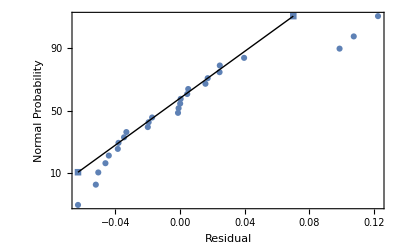

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
	(*    Задаване на извадките   *) 

y={0.22200,0.39500,0.42200,0.43700,0.42800,0.46700,0.44400,0.37800,0.49400,0.45600,0.45200,0.11200,0.43200,0.10100,0.23200,0.30600,0.09230,0.11600,0.07640,0.43900,0.09440,0.11700,0.07260,0.04120,0.25100,0.00002};
x11={7.3,8.7,8.8,8.1,9.0,8.7,9.3,7.6,10.0,8.4,9.3,7.7,9.8,7.3,8.5,9.5,7.4,7.8,7.7,10.3,7.8,7.1,7.7,7.4,7.3,7.6};
x21={0.0,0.0,0.7,4.0,0.5,1.5,2.1,5.1,0.0,3.7,3.6,2.8,4.2,2.5,2.0,2.5,2.8,2.8,3.0,1.7,3.3,3.9,4.3,6.0,2.0,7.8};
x31={0.0,0.3,1.0,0.2,1.0,2.8,1.0,3.4,0.3,4.1,2.0,7.1,2.0,6.8,6.6,5.0,7.8,7.7,8.0,4.2,8.5,6.6,9.5,10.9,5.2,20.7};
coord=Table[{x11[[n]],x21[[n]],x31[[n]],y[[n]]},{n,1,Length[y]}];
modlm=LinearModelFit[coord,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 1] Subscript[x, 2],Subscript[x, 1] Subscript[x, 3],Subscript[x, 2] Subscript[x, 3],Subscript[x, 1]^2,Subscript[x, 2]^2,Subscript[x, 3]^2},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},ConfidenceLevel->0.95];
Print ["           Получен  линеен модел:"]
Normal[modlm]
R2=modlm["RSquared"]
bands=modlm["MeanPredictionBands"];
fgn=Normal[modlm];
bands=modlm["MeanPredictionBands"];
Print ["          Таблица на доверителните интервали :"]
modlm["ParameterConfidenceIntervalTable"]
Show[Plot3D[fgn/.{Subscript[x, 1]->s,Subscript[x, 2]->p,Subscript[x, 3]-> 6},{s,7.1,10.3},{p,0,7.8},PlotRange->{-0.6,0.8},PlotStyle->Opacity[0.5],Mesh->None,ViewPoint->{1.8,-1.5,0.9},AxesLabel->{"x_1","x_2"," y(x_1,x_2,6)"}],Plot3D[bands/.Subscript[x, 1]->s/.Subscript[x, 2]->p/.Subscript[x, 3]->6,{s,7.1,10.3},{p,0,7.8},PlotStyle->Opacity[0.5],Mesh->None]]
ProbabilityScalePlot[modlm["FitResiduals"],"Normal",PlotMarkers->Automatic,FrameLabel->{"Residual","Normal Probability"}]
```

## Нелинеен регресионен анализ 3

FittedModel[ArcTan[22.9397+16.3693 Cos[2 x],-0.00323312 Cot[x]+32.8957 Cos[x] Sin[x]]]

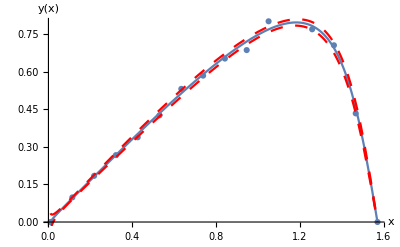

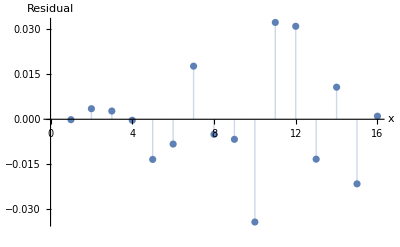

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
	(*    Задаване на извадката   *) 

dat={{0.01,0},{0.1141,0.09821},{0.2181,0.1843},{0.3222,0.2671},{0.4262,0.3384},{0.5303,0.426},{0.6343,0.5316},{0.7384,0.5845},{0.8424,0.6527},{0.9465,0.6865},{1.051,0.8015},{1.155,0.8265},{1.259,0.7696},{1.363,0.7057},{1.467,0.4338},{1.571,0}};
nlModel=NonlinearModelFit[dat,ArcTan[(c+d Cos[2 x]),(a Cot[x] Sin[x]^2-b Cot[x])],{{a,2},{b,0.1},{c,2},{d,2}},x,ConfidenceLevel->0.90]
bands=nlModel["MeanPredictionBands"];
Show[Plot[Normal[nlModel],{x,0.01,π/2},AxesLabel->{"x","y(x)"}],ListPlot[dat,PlotMarkers->Automatic],Plot[{bands[[1]],bands[[2]]}/.x->g,{g,0.01,π/2.},PlotStyle->{Red,Dashing[Medium]}]]
ListPlot[nlModel["FitResiduals"],Filling->Axis,AxesLabel->{"x","Residual"}]
```

## Задача 6.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 7.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 8.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
 Needs["HypothesisTesting`"]
```

## Задача 9.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 10.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 11.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 12.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 13.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 14.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 15.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 16.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 17.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 18.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 19.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 20.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 21.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 22.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 23.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 24.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 25.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 26.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 27.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 28.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 29.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```

## Задача 30.

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"]
```